N9.18 is a crude estimate of when you would reach terminal velocity, obtained just by setting g t = v_T. That is the intersection of a line with slope -g with the terminal velocity line that is horizontal below.

N9.19 is a plug-in, but we have gone far further and solved Problem N9D.4, which began by suggesting we have Mathematica or Wolfram Alpha do the following integral:

```mathematica
Integrate[1/(1-v^2/c^2),{v,0,vFinal}]
```

ConditionalExpression[c ArcTanh[vFinal/c], Re[c/vFinal]>1||Re[c/vFinal]<-1||c/vFinal∉ℝ]

```mathematica
c=N[200000/3600];
g=9.8
```

9.8

```mathematica
c
```

55.5556

The tanh function is sinh over cosh, where sinh x=(e^x-e^-x)/2 and cosh x=(e^x+e^-x)/2.

The arctanh relation to tanh is directly analogous to the arctan’s relation to tan.

So we take Tanh of both sides of the equation that Mathematica found us and get

```mathematica
v[t_]:=-c Tanh[g t / c]
```

Then we plot it:

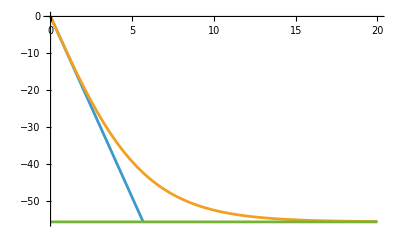

```mathematica
Plot[{-g t, v[t],-c},{t,0, 20},PlotRange->{{0,20},{0,-c}}]
```